## Calculation of the Case 1

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.124851}. NIntegrate obtained 3.57476×10^-11 and 5.0457×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.124851}. NIntegrate obtained 3.57916×10^-11 and 3.15795×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.124851}. NIntegrate obtained 3.03694×10^-11 and 3.46129×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

General::munfl: 0.180859 1.16431×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.139683 1.58672×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{6581.75,Null}

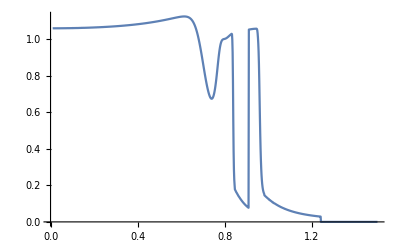

```mathematica
Clear["Global`*"]
w=1; NN=10; a1=0.85;  bn=0.85;
ef=6;  e0=0;  nn=1000;  T1=0.09;
v=N@Subdivide[0.01,1.5, nn];n0=N@Subdivide[0.01,90, nn];
jeA=Array[a1,1]; jeB=Array[bn,1];
For[qq=1,qq≤Length[v],qq++,
kj=Select[Select[x/.NSolve[v[[qq]]*Sin[x*(NN+1)]+w*Sin[x*NN]], FreeQ[#, _Complex] &],0<#<Pi&];
kj=DeleteDuplicates[kj];
dx=v[[qq]]+w*Cos[kj];
dy=w*Sin[kj]; 
En=Sqrt[v[[qq]]^2+w^2+2*v[[qq]]*w*Cos[kj]];
kM1=Transpose[Array[ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM2=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];
kM3=Transpose[Array[-ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM4=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];
Which[Length[kj]<NN, (* Divides berween Topological and Trivial case *)
jeA=Array[(-1)^(#-1)*(v[[qq]]/w)^(#-1)*a1&,NN];
nc=Norm[jeA];
jeA=jeA/(nc*Sqrt[2]);
jeB=Reverse[Array[(-1)^#*(v[[qq]]/w)^#*bn&,NN-1]];
jeB=Insert[jeB,bn,NN];
nc=Norm[jeB];
jeB=jeB/(nc*Sqrt[2]);
jeC=Flatten[Transpose[{Transpose[{jeA}],Transpose[{jeB}]}]];
jeV=Flatten[Transpose[{Transpose[{jeA}],-Transpose[{jeB}]}]];
xi=1/(Log[w]-Log[v[[qq]]]);
Ene=Abs[a1*v[[qq]]*bn*Exp[-(NN-1)/xi]];
En=Insert[En,Ene,NN];
H1=kM1; H2=kM3;
For[i=1,i<NN+1,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i<NN+1,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i<NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
HH=Insert[HH,jeC,2*NN-1];
HH=Insert[HH,jeV,2*NN] ;
,
True,
H1=kM1; H2=kM3;
For[i=1,i≤NN,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i≤NN,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i≤NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
];
For[i=1,i≤2*NN,i++,HH[[i]]=HH[[i]]/Norm[HH[[i]]]];
ψ=Inverse[HH];
Enn=Flatten[Transpose[{Transpose[{En}],-Transpose[{En}]}]];
Λ[ω_]:=T1^2*Sum[Abs[ψ[[1,i]]]^2/(ω-Enn[[i]]),{i,1,2*NN}];
Γ[ω_]:=2*Pi*T1^2*Sum[Abs[ψ[[1,i]]]^2*PDF[NormalDistribution[Enn[[i]],.02],ω],{i,1,2*NN}];
fun[ω_]:=1/(2*Pi)*Γ[ω]/((ω-e0-Λ[ω])^2+(Γ[ω])^2/4);
n0[[qq]]=NIntegrate[fun[ω],{ω, -∞,ef},
Method->{"LocalAdaptive",Method->"ClenshawCurtisRule"}]; 
(* ,
Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}*)
(* ,
Method->{"LocalAdaptive",Method->"ClenshawCurtisRule"} *)
(* ,Method->"MonteCarloRule" *)
(* ,Method->{"AdaptiveMonteCarlo",Method->"MonteCarloRule"} *)
(*,
 Method->"TrapezoidalRule" *)
(*,
Method->{"GlobalAdaptive",Method->{"TrapezoidalRule","Points"->5,"RombergQuadrature"->True},"SingularityDepth"->∞},MaxRecursion->100,PrecisionGoal->8*)
(*,
PrecisionGoal->10,MaxRecursion->1000,Method->{"GlobalAdaptive","SingularityDepth"->∞,"SymbolicProcessing"->0} *)
];//Timing
ListLinePlot[
Transpose[{v, n0}]]
```

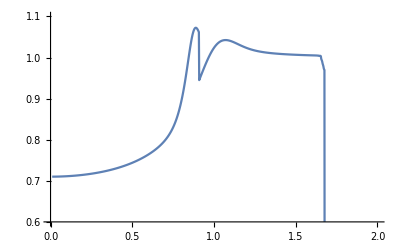

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0.6,1.1}] (* ,
PrecisionGoal->10,MaxRecursion->1000,Method->{"GlobalAdaptive","SingularityDepth"->∞,"SymbolicProcessing"->0} *)
```

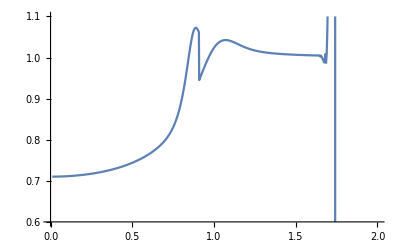

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0.6,1.1}](*,
Method->{"GlobalAdaptive",Method->{"TrapezoidalRule","Points"->5,"RombergQuadrature"->True},"SingularityDepth"->∞},MaxRecursion->100,PrecisionGoal->8*)
```

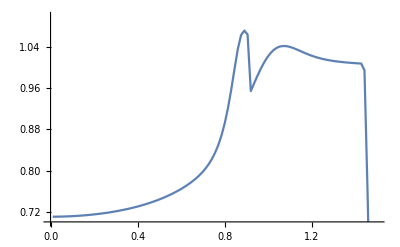

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0.7 ,1.1}]  (* ,
PrecisionGoal->10,MaxRecursion->1000,Method->{"LocalAdaptive","SingularityDepth"->∞,"SymbolicProcessing"->0} *)
```

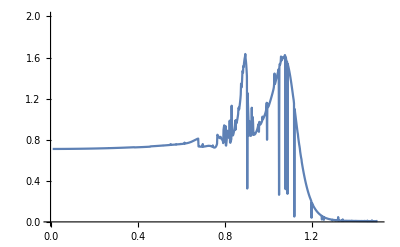

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0,2}] (* ,
 Method->"TrapezoidalRule"} *)
```

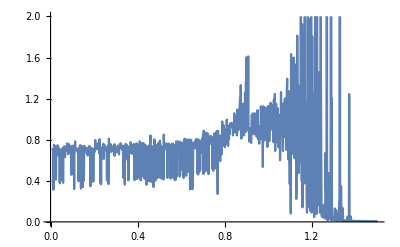

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0,2}] (* ,Method->"MonteCarloRule" *)
```

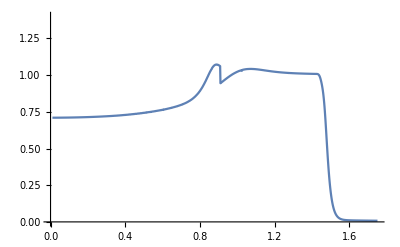

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0,1.4}] (* Local Adaptative Integration *)
```

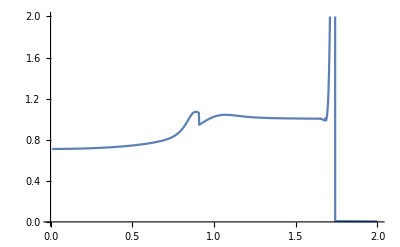

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0,2}] (*,
Method->{"GlobalAdaptive",Method->{"TrapezoidalRule","Points"->5,"RombergQuadrature"->True},"SingularityDepth"->∞},MaxRecursion->100,PrecisionGoal->8*)
```

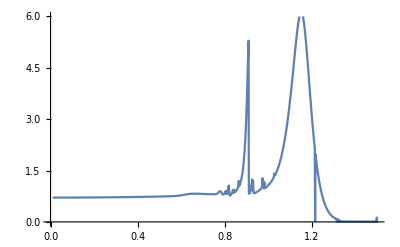

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0,6}] (* GlobalAdaptative INtegrate *)
```

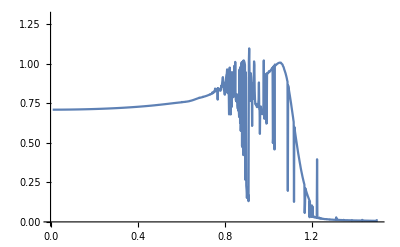

```mathematica
ListLinePlot[
Transpose[{v, n0}],PlotRange->{0,1.3}] (* Normal INtegrate *)
```

```mathematica
Clear["Global`*"]
w=1; NN=16; a1=0.85;  bn=0.85;
ef=6;  e0=0;  T1=0.01;
v=0.732634; 
jeA=Array[a1,1]; jeB=Array[bn,1];
kj=Select[Select[x/.NSolve[v*Sin[x*(NN+1)]+w*Sin[x*NN]], FreeQ[#, _Complex] &],0<#<Pi&];
kj=DeleteDuplicates[kj];
dx=v+w*Cos[kj];
dy=w*Sin[kj]; 
En=Sqrt[v^2+w^2+2*v*w*Cos[kj]];
kM1=Transpose[Array[ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM2=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];
kM3=Transpose[Array[-ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM4=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];
jeA=Array[(-1)^(#-1)*(v/w)^(#-1)*a1&,NN];
nc=Norm[jeA];
jeA=jeA/(nc*Sqrt[2]);
jeB=Reverse[Array[(-1)^#*(v/w)^#*bn&,NN-1]];
jeB=Insert[jeB,bn,10];
nc=Norm[jeB];
jeB=jeB/(nc*Sqrt[2]);
jeC=Flatten[Transpose[{Transpose[{jeA}],Transpose[{jeB}]}]];
jeV=Flatten[Transpose[{Transpose[{jeA}],-Transpose[{jeB}]}]];
xi=1/(Log[w]-Log[v]);
Ene=Abs[a1*v*bn*Exp[-(NN-1)/xi]];
En=Insert[En,Ene,NN];
H1=kM1; H2=kM3;
For[i=1,i<NN+1,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i<NN+1,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i<NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
HH=Insert[HH,jeC,2*NN-1];
HH=Insert[HH,jeV,2*NN] ;
For[i=1,i≤2*NN,i++,HH[[i]]=HH[[i]]/Norm[HH[[i]]]];
ψ=Inverse[HH];
Enn=Flatten[Transpose[{Transpose[{En}],-Transpose[{En}]}]]
Λ[ω_]:=T1^2*Sum[Abs[ψ[[1,i]]]^2/(ω-Enn[[i]]),{i,1,2*NN}]
Γ[ω_]:=2*Pi*T1^2*Sum[Abs[ψ[[1,i]]]^2*PDF[NormalDistribution[Enn[[i]],.01],ω],{i,1,2*NN}]
fun[ω_]:=1/(2*Pi)*Γ[ω]/((ω-e0-Λ[ω])^2+(Γ[ω])^2/4)
n0=NIntegrate[fun[ω],{ω, -∞,ef}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{1.7249,-1.7249,1.70178,-1.70178,1.6635,-1.6635,1.61041,-1.61041,1.54302,-1.54302,1.46198,-1.46198,1.3681,-1.3681,1.2623,-1.2623,1.14568,-1.14568,1.01951,-1.01951,0.885306,-0.885306,0.744969,-0.744969,0.601211,-0.601211,0.458958,-0.458958,0.33139,-0.33139,0.00497773,-0.00497773}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.080337}. NIntegrate obtained 1.58096 and 1.04219 for the integral and error estimates.

1.58096

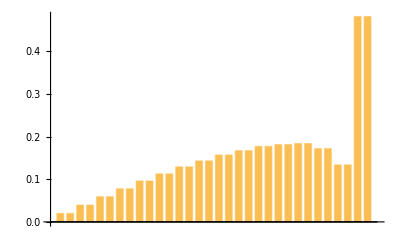

```mathematica
BarChart[Abs[ψ[[1]]]]
```

### Mesh varying two parameters

```mathematica
Clear["Global`*"]
w=1; NN=10; a1=0.85;  bn=0.85;
ef=4;  e0=0;  nn=200;  T1=N@Subdivide[0.015,0.2, nn];
v=N@Subdivide[0.001,1.5, nn];n0=ConstantArray[1, {Length[T1], Length[v]}] ;
jeA=Array[a1,1]; jeB=Array[bn,1];

For[qq=1,qq<Length[v],qq++,
kj=Select[Select[x/.NSolve[v[[qq]]*Sin[x*(NN+1)]+w*Sin[x*NN]], FreeQ[#, _Complex] &],0<#<Pi&];
kj=DeleteDuplicates[kj];
dx=v[[q]]+w*Cos[kj];
dy=w*Sin[kj]; 
En=Sqrt[v[[qq]]^2+w^2+2*v[[qq]]*w*Cos[kj]];
kM1=Transpose[Array[ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM2=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];
kM3=Transpose[Array[-ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM4=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];

Which[Length[kj]<NN, (* Divides berween Topological and Trivial case *)
jeA=Array[(-1)^(#-1)*(v[[qq]]/w)^(#-1)*a1&,NN];
nc=Norm[jeA];
jeA=jeA/(nc*Sqrt[2]);
jeB=Reverse[Array[(-1)^#*(v[[qq]]/w)^#*bn&,NN-1]];
jeB=Insert[jeB,bn,NN];
nc=Norm[jeB];
jeB=jeB/(nc*Sqrt[2]);
jeC=Flatten[Transpose[{Transpose[{jeA}],Transpose[{jeB}]}]];
jeV=Flatten[Transpose[{Transpose[{jeA}],-Transpose[{jeB}]}]];
xi=1/(Log[w]-Log[v[[qq]]]);
Ene=Abs[a1*v[[qq]]*bn*Exp[-(NN-1)/xi]];
En=Insert[En,Ene,NN];
H1=kM1; H2=kM3;
For[i=1,i<NN+1,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i<NN+1,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i<NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
HH=Insert[HH,jeC,2*NN-1];
HH=Insert[HH,jeV,2*NN] ;
,
True,
H1=kM1; H2=kM3;
For[i=1,i≤NN,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i≤NN,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i≤NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
];
For[i=1,i≤2*NN,i++,HH[[i]]=HH[[i]]/Norm[HH[[i]]]];
ψ=Inverse[HH];
Enn=Flatten[Transpose[{Transpose[{En}],-Transpose[{En}]}]];
For [tt=1,tt<Length[T1],tt++,
Λ[ω_]:=T1[[tt]]^2*Sum[Abs[ψ[[1,i]]]^2/(ω-Enn[[i]]),{i,1,2*NN}];
Γ[ω_]:=2*Pi*T1[[tt]]^2*Sum[Abs[ψ[[1,i]]]^2*PDF[NormalDistribution[Enn[[i]],.1],ω],{i,1,2*NN}];
fun[ω_]:=1/(2*Pi)*Γ[ω]/((ω-e0-Λ[ω])^2+(Γ[ω])^2/4);
n0[[qq,tt]]=NIntegrate[fun[ω],{ω, -∞,ef},
PrecisionGoal->10,MaxRecursion->1000,Method->{"GlobalAdaptive","SingularityDepth"->∞,"SymbolicProcessing"->0}];
];
];
meshgrid[x_List, y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
{xx, yy} = meshgrid[T1,v];
pts = Flatten[{xx, yy, n0}, {2, 3}];
ListPlot3D[pts, PlotRange -> All, AxesLabel -> {Abs[T],V/W}, InterpolationOrder -> 2, ColorFunction -> "Rainbow", Boxed -> False]
ListPlot[
Transpose[{v, n0[[30]]}]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

Part::pkspec1: The expression q cannot be used as a part specification.

```mathematica
ListPlot3D[pts, PlotRange -> All, AxesLabel -> {Abs[T],V/W}, InterpolationOrder -> 2, ColorFunction -> "Rainbow", Boxed -> False]
```

-Graphics3D-

```mathematica
v[[30]]
```

0.218355

```mathematica
Clear["Global`*"]
w=1; NN=10; a1=0.85;  bn=0.85;
ef=6;  e0=0;  nn=800;  T1=0.09;
v=N@Subdivide[0.001,1.5, nn];n0=ConstantArray[1, Length[v]] ;
jeA=Array[a1,1]; jeB=Array[bn,1];  
om=N@Subdivide[-5,5, nn]; npr= ConstantArray[1.0, {Length[v],Length[om]}];
For[qq=1,qq<Length[v],qq++,
kj=Select[Select[x/.NSolve[v[[qq]]*Sin[x*(NN+1)]+w*Sin[x*NN]], FreeQ[#, _Complex] &],0<#<Pi&];
kj=DeleteDuplicates[kj];
dx=v[[qq]]+w*Cos[kj];
dy=w*Sin[kj]; 
En=Sqrt[v[[qq]]^2+w^2+2*v[[qq]]*w*Cos[kj]];
kM1=Transpose[Array[ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM2=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];
kM3=Transpose[Array[-ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM4=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];
Which[Length[kj]<NN, (* Divides between Topological and Trivial case *)
jeA=Array[(-1)^(#-1)*(v[[qq]]/w)^(#-1)*a1&,NN];
nc=Norm[jeA];
jeA=jeA/(nc*Sqrt[2]);
jeB=Reverse[Array[(-1)^#*(v[[qq]]/w)^#*bn&,NN-1]];
jeB=Insert[jeB,bn,NN];
nc=Norm[jeB];
jeB=jeB/(nc*Sqrt[2]);
jeC=Flatten[Transpose[{Transpose[{jeA}],Transpose[{jeB}]}]];
jeV=Flatten[Transpose[{Transpose[{jeA}],-Transpose[{jeB}]}]];
xi=1/(Log[w]-Log[v[[qq]]]);
Ene=Abs[a1*v[[qq]]*bn*Exp[-(NN-1)/xi]];
En=Insert[En,Ene,NN];
H1=kM1; H2=kM3;
For[i=1,i<NN+1,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i<NN+1,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i<NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
HH=Insert[HH,jeC,2*NN-1];
HH=Insert[HH,jeV,2*NN] ;
,
True,
H1=kM1; H2=kM3;
For[i=1,i≤NN,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i≤NN,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i≤NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
];
For[i=1,i≤2*NN,i++,HH[[i]]=HH[[i]]/Norm[HH[[i]]]];
ψ=Inverse[HH];
Enn=Flatten[Transpose[{Transpose[{En}],-Transpose[{En}]}]];
σ=0.01;
Λ[ω_]:=T1^2*Sum[Abs[ψ[[1,i]]]^2/(ω-Enn[[i]]),{i,1,2*NN}];
Γ[ω_]:=2*Pi*T1^2*Sum[Abs[ψ[[1,i]]]^2*PDF[NormalDistribution[Enn[[i]],σ],ω],{i,1,2*NN}];
fun[ω_]:=1/(2*Pi)*Γ[ω]/((ω-e0-Λ[ω])^2+(Γ[ω])^2/4);
n0[[qq]]=NIntegrate[fun[ω],{ω, -∞,ef},
PrecisionGoal->10,MaxRecursion->1000,Method->{"GlobalAdaptive","SingularityDepth"->∞,"SymbolicProcessing"->0}];
npr[[qq]]=fun[om];
];
(*
{ListLinePlot[
Transpose[{v, n0[[All,1]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.09"],ListLinePlot[
Transpose[{v, n0[[All,2]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.08"],ListLinePlot[
Transpose[{v, n0[[All,3]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.07"],ListLinePlot[
Transpose[{v, n0[[All,4]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.06"],ListLinePlot[
Transpose[{v, n0[[All,5]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.05"],ListLinePlot[
Transpose[{v, n0[[All,6]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.04"],ListLinePlot[
Transpose[{v, n0[[All,7]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.03"],ListLinePlot[
Transpose[{v, n0[[All,8]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.02"],ListLinePlot[
Transpose[{v, n0[[All,9]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.01"]} *)
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::munfl: 9.5283×10^-9 6.432740427×10^-78197 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.5283×10^-9 1.744206185×10^-77871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.5283×10^-9 9.913214171×10^-77547 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0106478 and 1.56678×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0106551 and 1.57492×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0106627 and 1.48885×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

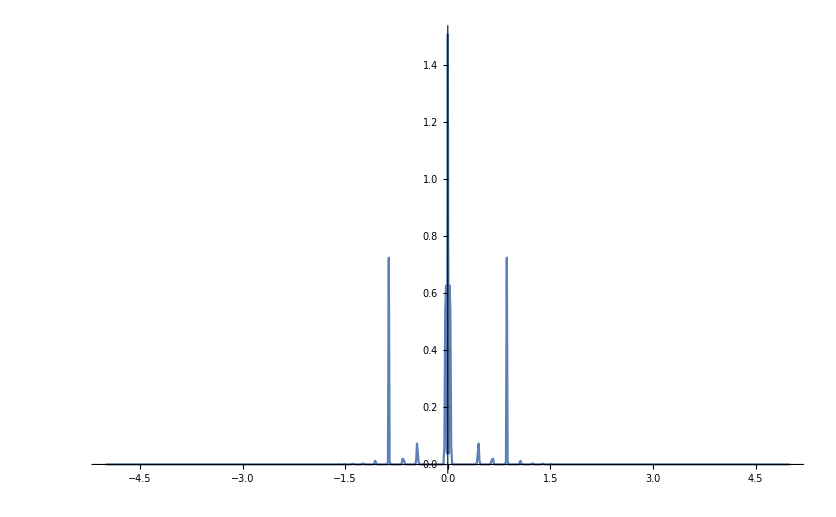

```mathematica
ListLinePlot[
Transpose[{om, npr[[360]]}],PlotRange->All]
```

```mathematica
v[[360]]
```

0.673676

## Calculation of n0 for the second case: Interaction with two molecules

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.080337}. NIntegrate obtained 1.1783 and 0.925529 for the integral and error estimates.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.080337}. NIntegrate obtained 1.17834 and 0.925579 for the integral and error estimates.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.080337}. NIntegrate obtained 1.17843 and 0.925685 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Cloud::timelimit: This computation has exceeded the time limit for your plan.

$Aborted

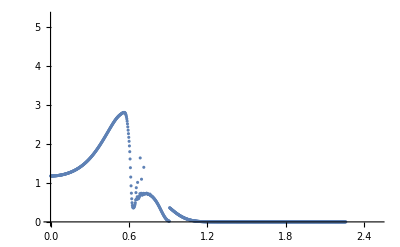

```mathematica
Clear["Global`*"]
w=1; NN=10; a1=0.85;  bn=0.85;
ef=6;  e0=0;  nn=1000;  T1A=0.01; T1B=0.01;
v=N@Subdivide[0.001,2.5, nn];n0=N@Subdivide[0.01,90, nn];
jeA=Array[a1,1]; jeB=Array[bn,1];
For[qq=1,qq≤Length[v],qq++,
kj=Select[Select[x/.NSolve[v[[qq]]*Sin[x*(NN+1)]+w*Sin[x*NN]], FreeQ[#, _Complex] &],0<#<Pi&];
kj=DeleteDuplicates[kj];
dx=v[[qq]]+w*Cos[kj];
dy=w*Sin[kj]; 
En=Sqrt[v[[qq]]^2+w^2+2*v[[qq]]*w*Cos[kj]];
kM1=Transpose[Array[ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM2=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];
kM3=Transpose[Array[-ⅈ*Sqrt[2/NN]*Cos[kj*#]*(dx*Tan[kj*#]-dy)/En&,NN]];
kM4=Transpose[Array[ⅈ*Sqrt[2/NN]*Sin[kj*#]&,NN]];

Which[Length[kj]<NN, (* Divides berween Topological and Trivial case *)
jeA=Array[(-1)^(#-1)*(v[[qq]]/w)^(#-1)*a1&,NN];
nc=Norm[jeA];
jeA=jeA/(nc*Sqrt[2]);
jeB=Reverse[Array[(-1)^#*(v[[qq]]/w)^#*bn&,NN-1]];
jeB=Insert[jeB,bn,NN];
nc=Norm[jeB];
jeB=jeB/(nc*Sqrt[2]);
jeC=Flatten[Transpose[{Transpose[{jeA}],Transpose[{jeB}]}]];
jeV=Flatten[Transpose[{Transpose[{jeA}],-Transpose[{jeB}]}]];
xi=1/(Log[w]-Log[v[[qq]]]);
Ene=Abs[a1*v[[qq]]*bn*Exp[-(NN-1)/xi]];
En=Insert[En,Ene,NN];
H1=kM1; H2=kM3;
For[i=1,i<NN+1,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i<NN+1,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i<NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
HH=Insert[HH,jeC,2*NN-1];
HH=Insert[HH,jeV,2*NN] ;
,
True,
H1=kM1; H2=kM3;
For[i=1,i≤NN,i++,H1=Transpose[Insert[H1 // Transpose, kM2[[All,i]],2*i]]];
For[i=1,i≤NN,i++,H2=Transpose[Insert[H2 // Transpose, kM4[[All,i]],2*i]]];
HH=H1;
For[i=1,i≤NN,i++,HH=Insert[HH,Transpose[ H2[[i]]],2*i]];
];
For[i=1,i≤2*NN,i++,HH[[i]]=HH[[i]]/Norm[HH[[i]]]];
ψ=Inverse[HH];
Enn=Flatten[Transpose[{Transpose[{En}],-Transpose[{En}]}]];
{Λ[ω_]:=Sum[(T1A^2*Abs[ψ[[1,i]]]^2+T1B^2*Abs[ψ[[2,i]]]^2)/(ω-Enn[[i]]),{i,1,2*NN}];}
{Γ[ω_]:=2*Pi*Sum[(T1A^2*Abs[ψ[[1,i]]]^2+T1B^2*Abs[ψ[[1,i]]]^2)*PDF[NormalDistribution[Enn[[i]],.1],ω],{i,1,2*NN}];}
{fun[ω_]:=1/(2*Pi)*Γ[ω]/((ω-e0-Λ[ω])^2+(Γ[ω])^2/4);}
{n0[[qq]]=NIntegrate[fun[ω],{ω, -∞,ef}];}
];
ListPlot[
Transpose[{v, n0}]]
```

General::munfl: 0.0000775075 2.73918621524×10^-2673 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000775075 1.10221021304×10^-1721 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000288072 4.13252857232×10^-2667 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

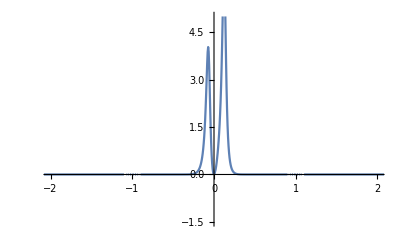

```mathematica
Plot[fun[ω],{ω,-10,10}, PlotRange -> {{-2, 2}, {-1.5, 5}}]
```

```mathematica
NIntegrate[PDF[NormalDistribution[Enn[[i-1]],0.009],ω],{ω,-10,10}, PrecisionGoal -> 100, WorkingPrecision -> 200]
```

NIntegrate::precw: The precision of the argument function (44.3269 ⅇ^(-6172.84 (0.965055+ω)^2)) is less than WorkingPrecision (200.).

1.0000000000000001732071345498289903835060489380966355883916391986474171897683960959934320531444117618314171268880176731064126480179430219696282095010157958111692929524260945127727566207579508170765827

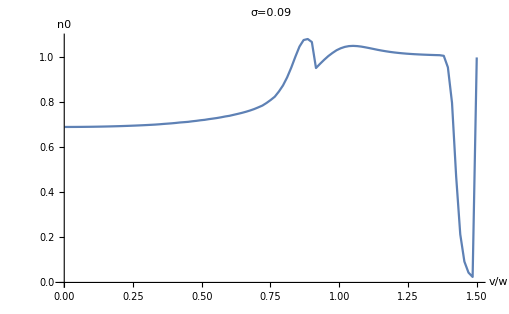
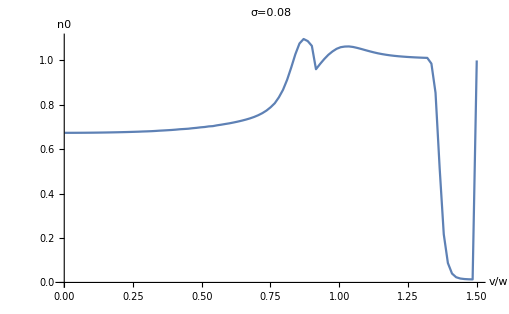
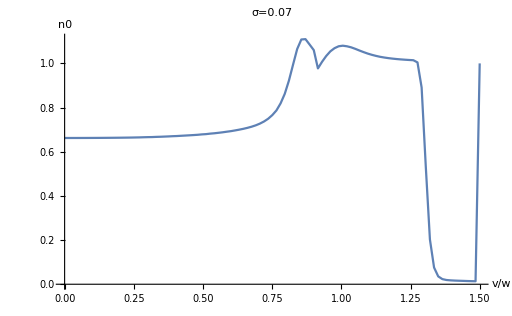
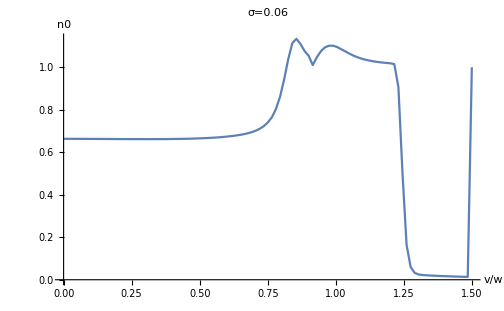
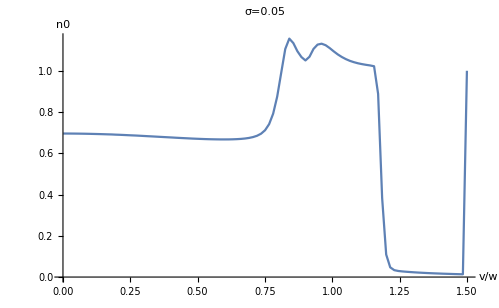
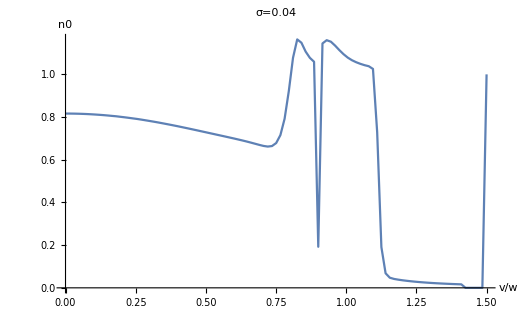
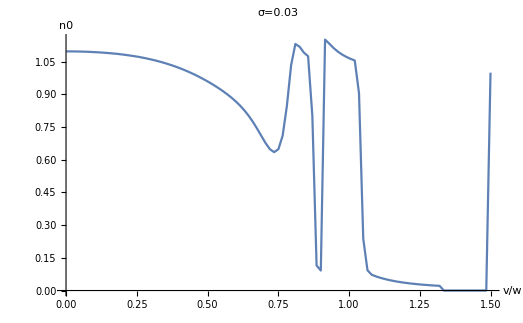
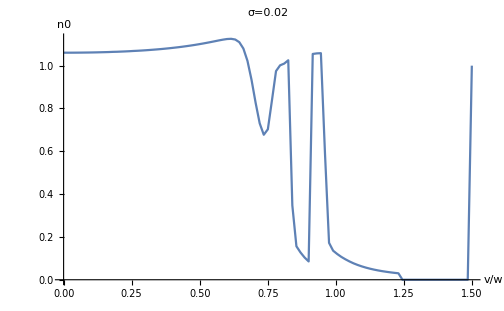

```mathematica
{ListLinePlot[
Transpose[{v, n0[[All,1]]}],AxesLabel->{"v"/"w","n0"},
PlotLabel->"σ=0.09"],ListLinePlot[
Transpose[{v, n0[[All,2]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.08"],ListLinePlot[
Transpose[{v, n0[[All,3]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.07"],ListLinePlot[
Transpose[{v, n0[[All,4]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.06"],ListLinePlot[
Transpose[{v, n0[[All,5]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.05"],ListLinePlot[
Transpose[{v, n0[[All,6]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.04"],ListLinePlot[
Transpose[{v, n0[[All,7]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.03"],ListLinePlot[
Transpose[{v, n0[[All,8]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.02"],ListLinePlot[
Transpose[{v, n0[[All,9]]}],AxesLabel->{"v"/"w","n0"},PlotLabel->"σ=0.01"]}
```

## SSH

```mathematica
Hssh [k_,v_,w_]:=Module[{h0},
h0={{0,v+w*Exp[-ⅈ*k]},{v+w*Exp[ⅈ*k],0}};
h0
];
```

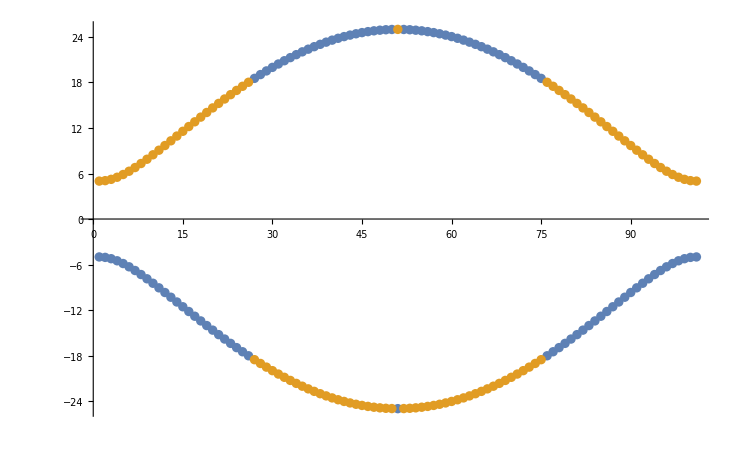

```mathematica
ListPlot[Transpose[Table[Sort[Eigenvalues[Hssh[k,10,15]]],{k,-Pi,Pi,2*Pi/100}]],PlotRange->All]
```

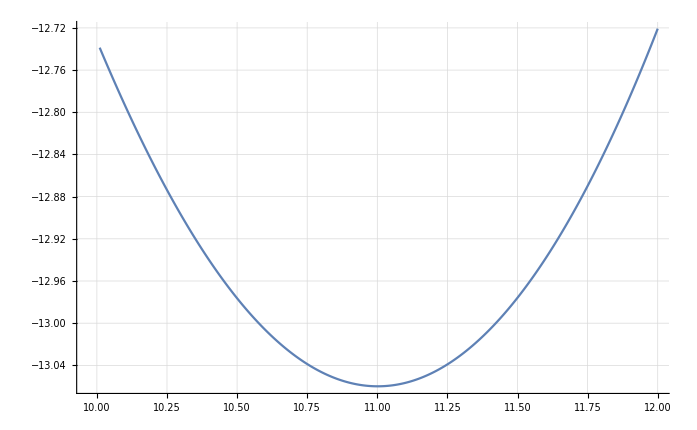

```mathematica
ClearAll["Global`*"]
v = 10; 
t0 [k_]:= (v+k)/2; t1[k_]:= (k-v)/2;
z[k_]:= t1[k]/t0[k]; α = 2.95;
e0 [k_]:= -4*t0[k]/Pi - (2*t0[k]/Pi)*(Log[4/z[k]]-0.5)z[k]^2+α*t0[k]^2*z[k]^2/2;
ListPlot[Table[Re[e0[k]],{k,10.01,12,1/1000}],PlotRange->All,Joined->True,DataRange->{10.01,12},GridLines->Automatic]
```

```mathematica
ListPlot[Table[Sqrt[(t0*(1+Cos[k])-t1*(1-Cos[k]))^2+(t0+t1)^2*(Sin[k])^2],{k,-Pi,Pi,2*Pi/100}],PlotRange->All]
```

-Graphics-

```mathematica
e0 [12]
```

14.4306-0.181818 ⅈ